# Gabarito da Primeira Prova de Transmissão 2010/2

```mathematica
Clear["Global`*"]
```

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotStyle-> Thick,Axes-> False,Frame-> True];
```

## Primeira Questão

Para a análise vamos considerar primeiro uma linha sem perdas, visto que apenas valores absolutos são considerados no cálculo da regulação
R=V_NL/V_FL-1 
onde V_NL representa o valor absoluto da tensão a vazio, e V_FLé o valor absoluto da tensão em pelna carga. Para ambas configurações de linha, a tensão em vazio é dada por 1/A, sendo A o elemento do quadripolo.
A=1/Cosh[θ] com  θ=ⅉω/cℓ
θ_0=5.76° para linha curta e θ_0=17.28° para a linha longa.

```mathematica
θ0=2 π 60 /(3 10^8)80000 (180/π);
θ1=2 π 60 /(3 10^8)240000(180/π);
```

O gráfico abaixo apresenta o Efeito Ferranti em função do ângulo elétrico da LT. Nesse gráfico é possível notar que para linha curta os valores são muito próximos a 1

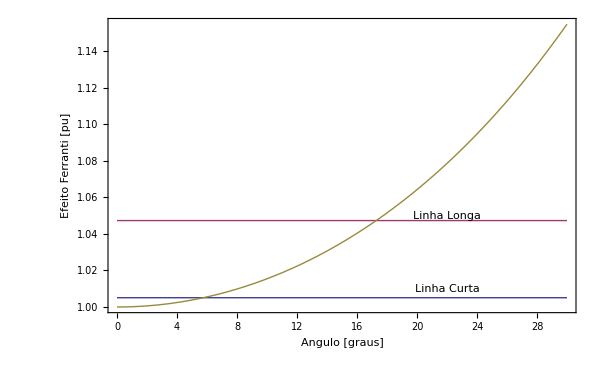

```mathematica
Plot[{1/Cos[θ0 Degree],1/Cos[θ1 Degree],1/Cos[x Degree]},{x,0,30 },PlotRange->All,PlotStyle-> Thick,Axes-> False,Frame-> True,FrameLabel-> {"Angulo [graus]", "Efeito Ferranti [pu]"},Epilog-> {Text["Linha Curta",{22.0, 1.01}],Text["Linha Longa",{22.0, 1.05}]}]
```

Admitindo - se que tanto a linha curta como a linha longa possuem tensão em plena carga semelhantes, algo como 0,95≤ V_FL≤1.05 temos, para a linha curta. A figura abaixo mostra a regulação de tensão para uma linha curta, onde pode-se ver que a regulação pode ser maior que uma linha longa dependendo qual a tensão a plena carga que a linha estará submetida. Desse resultado, pode-se notar que a regulação de uma linha longa pode ser menor que a encontrada numa linha curta.

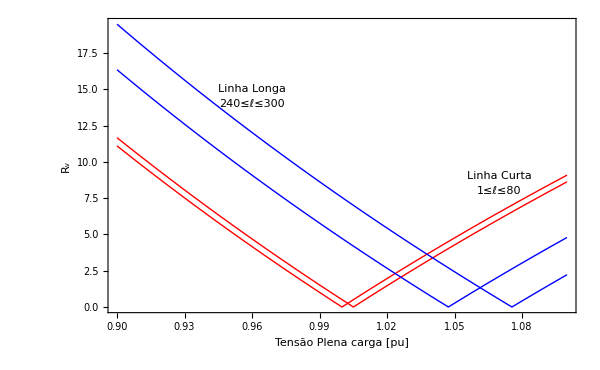

```mathematica
A0=1/Cos[θ0 Degree];
A1=1/Cos[θ1 Degree];
Plot[{100 Abs[(Sec[2 π 60./(3 10^8) 1000])/x-1],100 Abs[(Sec[2 π 60./(3 10^8) 80000])/x-1],100Abs[Sec[2 π 60./(3 10^8) 240000]/x-1],100Abs[Sec[2 π 60./(3 10^8) 300000]/x-1]
},{x,.9,1.1},PlotStyle-> {{Thick,Red},{Thick,Red},{Thick,Blue},{Thick,Blue}},FrameLabel->{"Tensão Plena carga [pu]","R_v"},Epilog->{ Text["Linha Curta",{1.07,9}], Text["1≤ℓ≤80 " ,{1.07,8}],Text["Linha Longa",{.96,15}], Text["240≤ℓ≤300 " ,{.96,14.}]}]
```

## Segunda Questão

A partir da manipulações do quadripolos é possível obter as expressões para a expressão da matriz de admitância Q01 e do quadripolo Q03. Os quadripolos são mostradas abaixo

```mathematica
a= Cosh[γ ℓ]; b=Zc Sinh[γ ℓ]; c=1/Zc Sinh[γ ℓ];
```

Para a expressão de Q01 basta resolver a expressão do quadripolo em função de i1 e i2

```mathematica
sol=Solve[{v1,i1}=={{a,b},{c,a}}.{v2,-i2},{i1,i2}]//FullSimplify;
```

```mathematica
Collect[i1/.sol,v1]
```

{(v1 Coth[ℓ γ])/Zc-(v2 Csch[ℓ γ])/Zc}

```mathematica
Collect[i2/.sol,v1]
```

{(v2 Coth[ℓ γ])/Zc-(v1 Csch[ℓ γ])/Zc}

Para a expressão de Q01 basta resolver a expressão do quadripolo em função de v1 e i2

```mathematica
sol1=Solve[{v1,i1}=={{a,b},{c,a}}.{v2,i2},{v1,i2}]//FullSimplify
```

{{v1→Sech[ℓ γ] (v2+i1 Zc Sinh[ℓ γ]),i2→i1 Sech[ℓ γ]-(v2 Tanh[ℓ γ])/Zc}}

## Terceira Questão

A potência nominal do circuito pode ser obtida a partir dos dados fornecidos no enunciado sobre os parâmetros unitários do circuito.

```mathematica
z=0.2+ⅉ 0.8;
y=I 6 10^-6;
ℓ=180.0;
γ=Sqrt[z y];
Zc=Sqrt[z/y];
```

```mathematica
a= Cosh[γ 300]; b=Zc Sinh[γ 300]; c=1/Zc Sinh[γ 300];
```

```mathematica
MatrixForm[q300={{a,b},{c,a}}]
```

(0.7912+0.0501934 ⅈ | 51.6305+224.101 ⅈ
-0.0000310213+0.001673 ⅈ | 0.7912+0.0501934 ⅈ)

```mathematica
c/c1
```

1.61188+0.0135841 ⅈ

```mathematica
a1=1+z y ℓ ℓ/2;
c1=y ℓ(1+ z ℓ y ℓ/4);
```

```mathematica
MatrixForm[Q1={{a1,z 180.},{c1,a1}}]
```

(0.92224+0.01944 ⅈ | 36.+144. ⅈ
-0.0000104976+0.00103801 ⅈ | 0.92224+0.01944 ⅈ)

```mathematica
FullForm[z ℓ]
```

Complex[36.,144.]

```mathematica
qt={{1,7+30 10^-3 2 π 60 I},{0,1}};
```

```mathematica
MatrixForm[qf=qt.Q1//N]
```

(0.910427+0.0265873 ⅈ | 42.2358+154.566 ⅈ
-0.0000104976+0.00103801 ⅈ | 0.92224+0.01944 ⅈ)

```mathematica
send=qt.{230 10^3/Sqrt[3], 360.896}
```

{135317.+4081.64 ⅈ,360.896+0. ⅈ}

```mathematica
Abs[send[[1]]]
```

135378.

```mathematica
vr=send[[1]]/qf[[1,1]]
```

148634.+142.623 ⅈ

```mathematica
Arg[send[[1]]]/π 180
```

1.72772

```mathematica
send[[2]]
```

360.896+0. ⅈ

```mathematica
3send[[1]] send[[2]]
```

1.46506×10^8+4.41914×10^6 ⅈ

```mathematica
is1=qf[[2,1]] vr
```

-1.70835+154.282 ⅈ

```mathematica
135.378 10^3 Exp[I 1.7277 Degree]Conjugate[ is1] 3
```

1.19564×10^6-6.26517×10^7 ⅈ

```mathematica
Zload=Re[Zc]
```

367.947

```mathematica
230^2/Re[Zc]
```

```mathematica
143.77065356700248 10^6/(Sqrt[3] 230 10^3)
```

360.896

```mathematica
q300.{ 230/Sqrt[3]10^3 ,360.896}
```

{123697.+87542.3 ⅈ,281.421+240.273 ⅈ}

Portanto, a potência do circuito é de 143 MW

```mathematica
v1=230 10^3/Sqrt[3];
```

```mathematica
curr=Flatten[{i1,i2}/.Solve[{v1,i1}=={{a,b},{c,a}}.{Zload i2,i2},{i1,i2}]]
```

{332.221+13.1758 ⅈ,307.365-121.268 ⅈ}

```mathematica
v2= Zload curr[[2]]
```

113094.-44620.1 ⅈ

```mathematica
s1=Sqrt[3] v1 Conjugate[curr[[1]]]
```

7.64108×10^7-3.03043×10^6 ⅈ

```mathematica
s2=Sqrt[3] v2 Conjugate[curr[[2]]]
```

6.95803×10^7+0. ⅈ

```mathematica
Δs=s1-s2
```

6.83052×10^6-3.03043×10^6 ⅈ

Há também as perdas no transformador

```mathematica
ptrafo=3 7 curr[[1]]Conjugate[curr[[1]]]
```

2.32143×10^6+0. ⅈ

```mathematica
Re[Δs]+ptrafo
```

9.15195×10^6+0. ⅈ

As perdas no circuito são de 9 MW

As perdas no circuito são de 9 MW

```mathematica
μ=4 π 10^-7;
ϵ=8.854 10^-12;
```

## Quarta Questão

A potência nominal do circuito pode ser obtida a partir dos dados fornecidos no enunciado sobre os parâmetros unitários do circuito.

```mathematica
z=0.015+ⅉ 0.27;
y=I 6.1 10^-6;
ℓ=170.0;
```

```mathematica
a= 1+z ℓ  y ℓ/2;
b= z ℓ;
c=y ℓ(1+ z ℓ y ℓ/4);
```

```mathematica
MatrixForm[q={{a,b},{c,a}}]
```

(0.976201+0.00132217 ⅈ | 2.55+45.9 ⅈ
-6.85548×10^-7+0.00102466 ⅈ | 0.976201+0.00132217 ⅈ)

```mathematica
MatrixForm[Q2=q.q]
```

(0.905933+0.00516283 ⅈ | 4.85725+89.622 ⅈ
-4.04802×10^-6+0.00200055 ⅈ | 0.905933+0.00516283 ⅈ)

```mathematica
Abs[Q2]
```

{{0.905947,89.7535},{0.00200055,0.905947}}

```mathematica
Arg[Q2]/Degree
```

{{0.32652,86.8978},{90.1159,0.32652}}

```mathematica
i=800.0 10^3/(Sqrt[3] 525.0)
```

879.772

```mathematica
out={525.0 10^3/Sqrt[3], i Exp[I ArcCos[.95]]}
```

{303109.,835.783+274.709 ⅈ}

```mathematica
send=Q2.out
```

{254036.+77803.8 ⅈ,754.518+859.566 ⅈ}

```mathematica
Abs[send]
```

{265683.,1143.74}

```mathematica
a1=1+z y ℓ ℓ/2;
c1=y ℓ(1+ z ℓ y ℓ/4);
```

```mathematica
MatrixForm[Q1={{a1,z 180.},{c1,a1}}]
```

(0.92224+0.01944 ⅈ | 36.+144. ⅈ
-0.0000104976+0.00103801 ⅈ | 0.92224+0.01944 ⅈ)

```mathematica
FullForm[z ℓ]
```

Complex[36.,144.]

```mathematica
qt={{1,7+30 10^-3 2 π 60 I},{0,1}};
```

```mathematica
MatrixForm[qf=qt.Q1//N]
```

(0.910427+0.0265873 ⅈ | 42.2358+154.566 ⅈ
-0.0000104976+0.00103801 ⅈ | 0.92224+0.01944 ⅈ)

```mathematica
send=qt.{230 10^3/Sqrt[3], 360.896}
```

{135317.+4081.64 ⅈ,360.896+0. ⅈ}

```mathematica
Abs[send[[1]]]
```

135378.

```mathematica
vr=send[[1]]/qf[[1,1]]
```

148634.+142.623 ⅈ

```mathematica
Arg[send[[1]]]/π 180
```

1.72772

```mathematica
send[[2]]
```

360.896+0. ⅈ

```mathematica
3send[[1]] send[[2]]
```

1.46506×10^8+4.41914×10^6 ⅈ

```mathematica
is1=qf[[2,1]] vr
```

-1.70835+154.282 ⅈ

```mathematica
135.378 10^3 Exp[I 1.7277 Degree]Conjugate[ is1] 3
```

1.19564×10^6-6.26517×10^7 ⅈ

```mathematica
Zload=Re[Zc]
```

367.947

```mathematica
230^2/Re[Zc]
```

```mathematica
143.77065356700248 10^6/(Sqrt[3] 230 10^3)
```

360.896

```mathematica
q300.{ 230/Sqrt[3]10^3 ,360.896}
```

{123697.+87542.3 ⅈ,281.421+240.273 ⅈ}

Portanto, a potência do circuito é de 143 MW

```mathematica
v1=230 10^3/Sqrt[3];
```

```mathematica
curr=Flatten[{i1,i2}/.Solve[{v1,i1}=={{a,b},{c,a}}.{Zload i2,i2},{i1,i2}]]
```

{332.221+13.1758 ⅈ,307.365-121.268 ⅈ}

```mathematica
v2= Zload curr[[2]]
```

113094.-44620.1 ⅈ

```mathematica
s1=Sqrt[3] v1 Conjugate[curr[[1]]]
```

7.64108×10^7-3.03043×10^6 ⅈ

```mathematica
s2=Sqrt[3] v2 Conjugate[curr[[2]]]
```

6.95803×10^7+0. ⅈ

```mathematica
Δs=s1-s2
```

6.83052×10^6-3.03043×10^6 ⅈ

Há também as perdas no transformador

```mathematica
ptrafo=3 7 curr[[1]]Conjugate[curr[[1]]]
```

2.32143×10^6+0. ⅈ

```mathematica
Re[Δs]+ptrafo
```

9.15195×10^6+0. ⅈ

As perdas no circuito são de 9 MW

As perdas no circuito são de 9 MW

```mathematica
μ=4 π 10^-7;
ϵ=8.854 10^-12;
```